# SEMINARSKA NALOGA - Mathematica

Tamara Pogačar, Praktična Matematika, FMF UL

## FIZIKA - Izpitna pola 2, Petek, 9. junij 2017

vir: https://www.ric.si/mma/M171-411-1-2/2017101014420471/

## 2. MEHANIKA

Kroglico z maso 0,10 kg spustimo v prosto padanje z višine H = 2,0 m nad tlemi. Pri vseh vprašanjih te naloge privzemite, da je zračni upor zanemarljiv in da je kroglica dovolj majhna, da njenih dimenzij ni treba upoštevati.

```mathematica
ClearAll[m, H, gg]
m = 0.1;
H = 2;
gg = 9.81;
```

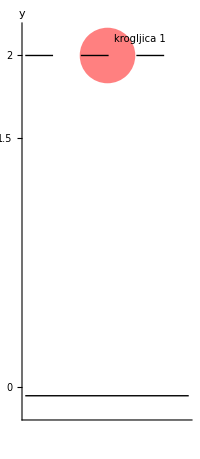

```mathematica
Graphics[ {{PointSize[0.1],Pink,Point[{0.5, H}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, H +0.1}]
},
{Dashing[{0.05, 0.05}], Line[{{0, H}, {1, H}}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0,h0, H}}]
```

#### 2.1.

Izračunajte, koliko časa pada kroglica do tal.

```mathematica
ClearAll[casDoTal]
casDoTal = Sqrt[(2*H)/gg]
```

0.638551

#### 2.2.

Izračunajte hitrost, s katero kroglica trči ob tla.

```mathematica
ClearAll[hitrostObTrku]
hitrostObTrku = 0 - gg * casDoTal
```

-6.26418

Kroglica se od tal odbije navpično navzgor. Ker odboj ni popolnoma prožen, je hitrost takoj po odboju od tal nekoliko manjša, kot je bila tik pred odbojem. Hitrost kroglice po odboju je tolikšna, da se lahko dvigne do največ h0 = 1,5 m  nad tlemi.

```mathematica
ClearAll[h0]
h0 = 1.5;
```

#### 2.3.

Izračunajte, kolikšna je hitrost kroglice takoj po odboju od tal.

```mathematica
ClearAll[hitrostPoOdboju]
hitrostPoOdboju = Sqrt[2*gg*h0]
```

5.42494

```mathematica
vektorHitrosti[visina_, hitrost_]:=
Arrow[{{0.5, visina},{0.5, (visina + hitrost/20)}}]
```

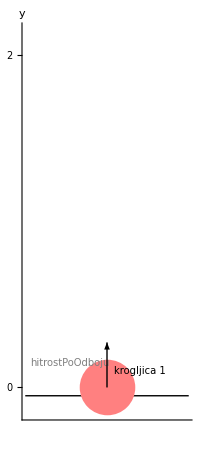

```mathematica
Graphics[ {
{PointSize[0.1],Pink,Point[{0.5, 0}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, 0 +0.1}]
},
{vektorHitrosti[0, hitrostPoOdboju], Text[Style["hitrostPoOdboju",Gray, FontSize->10], {0.275, 0.15}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0, H}}]
```

#### 2.4.

Izračunajte, za koliko je kinetična energija kroglice takoj po odboju od tal manjša od kinetične energije tik pred odbojem kroglice.

```mathematica
ClearAll[spremembaEnergije]
spremembaEnergije = (m*(hitrostPoOdboju^2-hitrostObTrku^2))/2
```

-0.4905

V istem trenutku (t = 0), kot se prva kroglica odbije od tal, spustimo prosto padati drugo kroglico z višine h0 = 1,5 m (to je višina, do katere bi se dvignila prva kroglica po odboju). Ker se kroglici gibljeta po isti premici, v trenutku t = 0,277 s trčita na neki višini od tal (hT ). Privzemite, da se kroglici ob trku sprimeta. Masa druge kroglice je enaka masi prve kroglice.

```mathematica
ClearAll[t]
t = 0.277;
```

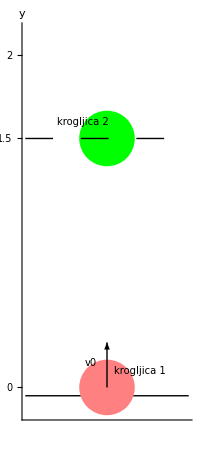

```mathematica
Graphics[ {{PointSize[0.1],Green,Point[{0.5, h0}], Text[Style["krogljica 2",Black, FontSize-> 10], {0.35, h0 +0.1}]
},
{PointSize[0.1],Pink,Point[{0.5, 0}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, 0 +0.1}]
},
{vektorHitrosti[0, hitrostPoOdboju], Text[Style["v0", FontSize->10], {0.4, 0.15}]},
{Dashing[{0.05, 0.05}], Line[{{0, h0}, {1, h0}}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0,h0, H}}]
```

Slika 1: V trenutko, ko se prva krogljica odbije od tal, z višine 1,5 m nad tlemi spustimo drugo, enako kroglico.

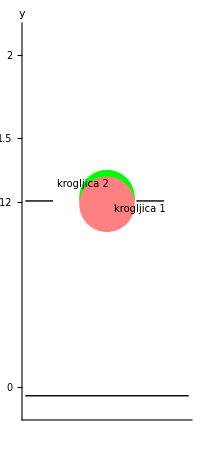

```mathematica
Graphics[ {{PointSize[0.1],Green,Point[{0.5, hT+0.02}], Text[Style["krogljica 2",Black, FontSize-> 10], {0.35, hT +0.1}]
},
{PointSize[0.1],Pink,Point[{0.5, hT-0.02}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, hT-0.05}]
},
{Dashing[{0.05, 0.05}], Line[{{0, hT}, {1, hT}}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0,Round[hT, 0.01], h0, H}}]
```

Slika 2: Kroglici se v nekem trenutku srečata na neki višini od tal in neprožno trčita.

#### 2.5.

Izračunajte hitrosti obeh kroglic tik pred trkom in višino, na kateri se srečata.

```mathematica
ClearAll[v1, v2]
v1 = hitrostPoOdboju - gg*t
v2 = -gg*t
hT = h0 - (gg*t^2)/2
```

2.70757

-2.71737

1.12364

#### 2.6.

Kolikšni sta skupna hitrost in skupna kinetična energija kroglic takoj po trku? Odgovor utemeljite.

```mathematica
ClearAll[skupnaKineticnaEnergija, skupnaHitrost]
skupnaHitrost = (m(v1 + v2))/(2*m)
skupnaKineticnaEnergija = (m*skupnaHitrost^2)/2
```

-0.0048988

1.19991×10^-6

Ker sta hitrosti žogic tik pred trkom skoraj enaki, je po trku njuna skupna hitrost približek 0 (nič) v smeri druge žočice (navzdol, tj. v negativni smeri), saj je bila tik pred trkom za odtenek hitrejša. Ker je kinetična energija telesa s stalno maso odvisna zgolj od njene hitrosti, je v našem primeru (ko je hitrost proaktično 0),  tudi kinetična energija žogic tik po trgu zelo blizu 0.

#### 2.7.

Izračunajte razliko med skupno začetno potencialno energijo obeh kroglic (preden ju spustimo v padanje) in njuno skupno potencialno energijo, ki jo imata kroglici takoj po trku druga ob drugo. (Potencialne energije lahko računate glede na tla, zračni upor pa je ves čas zanemarljiv.)

```mathematica
ClearAll[zacetnaPotencialna1,zacetnaPotencialna2, koncnaPotencialna1, koncnaPotencialna2,  razlikaPotencialnihEnergij]
razlikaPotencialnihEnergij[zacetnaVisina1_, zacetnaVisina2_, visinaTrka_]:=Module[{zacetnaPotencialna1, zacetnaPotencialna2, koncnaPotencialna1, koncnaPotencialna2},
zacetnaPotencialna1 =m*gg*zacetnaVisina1;
zacetnaPotencialna2 = m*gg*zacetnaVisina2;
koncnaPotencialna1 = m*gg*visinaTrka;
koncnaPotencialna2 =m*gg*visinaTrka;
razlikaPotencialnihEnergij = zacetnaPotencialna1 + zacetnaPotencialna2 - koncnaPotencialna1 - koncnaPotencialna2]
razlikaPotencialnihEnergij[H, h0, hT]
```

1.22891

Poskus ponovimo tako, da v istem trenutku (t = 0), kot se prva kroglica odbije od tal, spustimo v prosto padanje drugo kroglico (masi kroglic sta enaki) s prvotne višine H = 2,0 m nad tlemi. Kroglici se spet gibljeta po isti premici in v nekem trenutku t trčita na neki višini od tal (h). Pri trku se sprimeta.

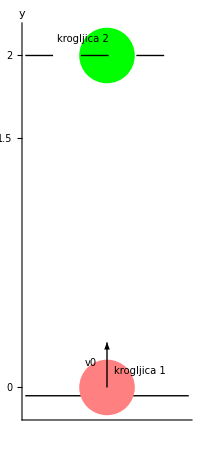

```mathematica
Graphics[ {{PointSize[0.1],Green,Point[{0.5, H}], Text[Style["krogljica 2",Black, FontSize-> 10], {0.35, H +0.1}]
},
{PointSize[0.1],Pink,Point[{0.5, 0}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, 0 +0.1}]
},
{vektorHitrosti[0, hitrostPoOdboju], Text[Style["v0", FontSize->10], {0.4, 0.15}]},
{Dashing[{0.05, 0.05}], Line[{{0, H}, {1, H}}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0,h0, H}}]
```

Slika: drugo krogljico spustimo z višine H = 2 v trenutku, ko se 1. krogljica odbije od tal.

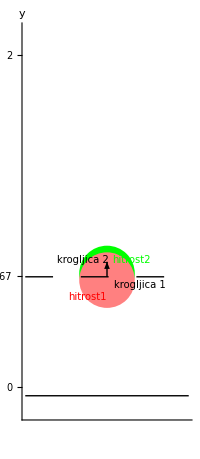

```mathematica
Graphics[ {{PointSize[0.1],Green,Point[{0.5, h+0.02}], Text[Style["krogljica 2",Black, FontSize-> 10], {0.35, h +0.1}]
},
{vektorHitrosti[h, hitrost2], Text[Style["hitrost2",Green,  FontSize->10], {0.65, h+0.1}]},
{PointSize[0.1],Pink,Point[{0.5, h-0.02}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, h-0.05}]
},
{vektorHitrosti[h, hitrost1], Text[Style["hitrost1", Red, FontSize->10], {0.38,h-0.12}]},
{Dashing[{0.05, 0.05}], Line[{{0, h}, {1, h}}]},
Line[{{0, -0.05}, {1, -0.05}}]
},
Axes->{True}, AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{0, 1}, {-0.15, H+0.15}}, Ticks->{False, {0,Round[h, 0.01], H}}]
```

#### 2.8.

Izračunajte, čez koliko časa se kroglici srečata, ter navedite, v katero smer (navzgor ali navzdol) in s kolikšno hitrostjo se takoj po trku giblje sprimek kroglic v tem primeru. Odgovor utemeljite.

```mathematica
ClearAll[t, hitrost1, hitrost2]
t = H/hitrostPoOdboju
hitrost1 = hitrostPoOdboju-gg*t;
hitrost2 = -gg*t;
hitrostSkupna = (hitrost1 + hitrost2)/2
```

0.368668

-0.904157

Kroglici se srečata po 0,37 s in se takoj po trku gibljeta v smeri druge krogljice (navzdol) s hitrostjo 0,9 m/s.

```mathematica
ClearAll[h]
h= (gg*t^2)/2
```

0.666667

## Animacije:

### Ena krogljica - spustimo jo z višine H = 2:

Prikaz, kje se nahaja žogica ob poljubnem času.

```mathematica
Manipulate[Graphics[ {{PointSize[0.1],Pink,Point[{0.5,  (gg*t^2)/2}], Text[Style["krogljica 1",Black, FontSize-> 10], {0.7, (gg*t^2)/2 +0.1}]
},
{Dashing[{0.05, 0.05}], Line[{{0, (gg*t^2)/2}, {1, (gg*t^2)/2}}]},
Line[{{-0.15, -0.05}, {1, -0.05}}]
},
Axes->{True},  AxesLabel->y, AxesStyle->{Thick, Thin}, PlotRange->{{-0.15, 1}, {-0.15, 2.15}}, Ticks->{False, {0,h0, Round[(gg*t^2)/2, 0.01]}}], {t, casDoTal, 0}]
```